```mathematica
goodgraph[graph_]:=Block[{vd=And@@Map[#>2&,VertexDegree[graph]]},Piecewise[{{Block[{vc=VertexConnectivity[graph]},Piecewise[{{Block[{ec=EdgeConnectivity[graph]},Piecewise[{{Block[{cyd=Length[FindCycle[graph,∞,3]]},Piecewise[{{True, cyd==3}, {False, cyd≠3}}]], ec>1}, {False, ec≤1}}]], vc>1}, {False, vc≤1}}]], vd}, {False, ¬vd}}]]
gedges[graph_]:=Block[{ged=(Length[EdgeList[graph]]≤12)},Piecewise[{{goodgraph[graph], ged}, {False, ¬ged}}]]
lt30= Select[GraphData[;;30],gedges[GraphData[#]]&];
```

```mathematica
cprop[x_]:=Block[{g=Quiet[GraphData[RandomChoice[lt30]]]},
Block[{g1=Graph[Map[Piecewise[{{#[[1]]->#[[2]], RandomInteger[1]==0}, {#[[2]]->#[[1]], True}}]&,EdgeList[g]]],g2=Graph[Map[Piecewise[{{#[[1]]->#[[2]], RandomInteger[1]==0}, {#[[2]]->#[[1]], True}}]&,EdgeList[g]]]},
Block[{vc1=VertexConnectivity[g1],ec1=VertexConnectivity[g1],vc2=VertexConnectivity[g2],ec2=VertexConnectivity[g2]},
Block[{numcy1=Length[FindCycle[g1,∞,All]],numcy2=Length[FindCycle[g2,∞,All]]},
Map[Boole,{(vc1==vc2)||((vc1<vc2)&&(numcy1<numcy2))||((vc1>vc2)&&(numcy1>numcy2)),
(ec1==ec2)||((ec1<ec2)&&(numcy1<numcy2))||((ec1>ec2)&&(numcy1>numcy2)),
(¬((vc1<vc2)&&(ec1<ec2))||¬((vc1>vc2)&&(ec1>ec2)))||((vc1<vc2)&&(ec1<ec2)&&(numcy1<numcy2))||((vc1>vc2)&&(ec1>ec2)&&(numcy1>numcy2))}]]]]]
(*{EdgeCount[g],VertexCount[g],vc,ec,numcy}]]*)
```

```mathematica
cprop2[x_]:=Block[{g=Quiet[GraphData[RandomChoice[lt30]]]},
Block[{g1=Graph[Map[Piecewise[{{#[[1]]->#[[2]], RandomInteger[1]==0}, {#[[2]]->#[[1]], True}}]&,EdgeList[g]]],g2=Graph[Map[Piecewise[{{#[[1]]->#[[2]], RandomInteger[1]==0}, {#[[2]]->#[[1]], True}}]&,EdgeList[g]]]},
Block[{vc1=VertexConnectivity[g1],ec1=VertexConnectivity[g1],vc2=VertexConnectivity[g2],ec2=VertexConnectivity[g2]},
Block[{numcy1=Length[FindCycle[g1,∞,All]],numcy2=Length[FindCycle[g2,∞,All]]},
Map[Boole,{(vc1==vc2)||((vc1<vc2)&&(numcy1≤numcy2))||((vc1>vc2)&&(numcy1≥numcy2)),
(ec1==ec2)||((ec1<ec2)&&(numcy1≤numcy2))||((ec1>ec2)&&(numcy1≥numcy2)),
(¬((vc1<vc2)&&(ec1<ec2))||¬((vc1>vc2)&&(ec1>ec2)))||((vc1<vc2)&&(ec1<ec2)&&(numcy1≤numcy2))||((vc1>vc2)&&(ec1>ec2)&&(numcy1≥numcy2))}]]]]]
```

```mathematica
cprop[0]
```

{1,1,1}

```mathematica
many[xy_]:=Map[Last,Tally[Join[Map[PadLeft[IntegerDigits[#,2],3]&,Range[0,7]],Table[cprop[x],{x,1,1000}]]]]-ConstantArray[1,8]
Timing[many[1]]
```

{3.76733,{0,8,0,0,0,0,0,992}}

```mathematica
many2[xy_]:=Map[Last,Tally[Join[Map[PadLeft[IntegerDigits[#,2],3]&,Range[0,7]],Table[cprop2[x],{x,1,1000}]]]]-ConstantArray[1,8]
Timing[many2[1]]
```

{3.6917,{0,5,0,0,0,0,0,995}}

```mathematica
20*60*4/3.46463
```

```mathematica
Timing[ParallelCombine[many2,Range[10],Plus]]
```

{0.46979,{0,50,0,0,0,0,0,7950}}

```mathematica
1385*1000
```

1385000

```mathematica
Timing[ParallelCombine[pk,Range[1385],Plus]]
```

{1.97227,{0,190,0,0,0,0,0,27810}}

```mathematica
Timing[ParallelCombine[pk,Range[1385],Plus]]
```

{2.18282,{0,184,0,0,0,0,0,27816}}

```mathematica
Timing[ParallelCombine[many,Range[1385],Plus]]
```

{2.13394,{0,180,0,0,0,0,0,27820}}

```mathematica
Timing[ParallelCombine[many,Range[1385],Plus]]
```

{25.1039,{0,1940,0,0,0,0,0,278060}}

```mathematica
Timing[ParallelCombine[many,Range[100],Plus]]
```

{11.5788,{0,807,0,0,0,0,0,119193}}

```mathematica
Timing[ParallelCombine[many,Range[100],Plus]]
```

{9.9463,{0,840,0,0,0,0,0,119160}}

```mathematica
Timing[ParallelCombine[many,Range[100],Plus]]
```

{9.67652,{0,844,0,0,0,0,0,119156}}

```mathematica
Timing[ParallelCombine[many,Range[100],Plus]]
```

{10.0362,{0,833,0,0,0,0,0,119167}}

```mathematica
Timing[ParallelCombine[many,Range[100],Plus]]
```

{9.83055,{0,820,0,0,0,0,0,119180}}

```mathematica
Timing[ParallelCombine[many,Range[100],Plus]]
```

{9.86857,{0,878,0,0,0,0,0,119122}}

```mathematica
Timing[ParallelCombine[many,Range[100],Plus]]
```

{9.5685,{0,822,0,0,0,0,0,119178}}

```mathematica
Timing[ParallelCombine[many,Range[100],Plus]]
```

{9.81705,{0,788,0,0,0,0,0,119212}}

```mathematica
Timing[ParallelCombine[many,Range[100],Plus]]
```

{9.70062,{0,795,0,0,0,0,0,119205}}

```mathematica
Timing[ParallelCombine[many,Range[100],Plus]]
```

{9.73405,{0,789,0,0,0,0,0,119211}}

```mathematica
Timing[ParallelCombine[many,Range[100],Plus]]
```

{9.9416,{0,825,0,0,0,0,0,119175}}

```mathematica
Timing[ParallelCombine[many,Range[100],Plus]]
```

{9.71073,{0,798,0,0,0,0,0,119202}}

```mathematica
Timing[ParallelCombine[many,Range[100],Plus]]
```

{9.75279,{0,859,0,0,0,0,0,119141}}

```mathematica
Map[{VertexConnectivity[GraphData[#]],EdgeConnectivity[GraphData[#]]}&,lt30]
```

{{3,3},{2,3},{3,3},{3,3},{3,3},{2,3},{2,3},{2,3},{2,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{4,4},{2,3},{2,3},{2,3},{2,3},{2,3},{2,3},{2,3},{2,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,4},{3,4},{3,4},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4},{3,3},{3,3},{3,3},{4,4},{3,3},{3,3},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{3,3},{3,3},{3,3},{4,4},{4,4},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{3,3},{3,3},{3,3},{3,3},{2,3},{3,3},{3,3},{3,3},{3,3},{2,2},{4,4},{4,4},{5,5},{4,5},{4,4},{4,4},{6,6},{4,4},{6,6},{6,6},{5,5},{4,5},{5,5},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{5,5},{5,5},{5,5},{4,5},{5,5},{5,5},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{5,5},{6,6},{7,7},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{4,4},{4,4},{5,5},{5,5},{4,4},{4,4},{4,4},{5,5},{5,5},{5,5},{5,5},{6,6},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{4,4},{4,4},{5,5},{5,5},{5,5},{5,5},{6,6},{5,5},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4},{5,5},{3,3},{3,3},{2,2},{2,2},{2,2},{2,2},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{2,2},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{2,2},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{2,2},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{2,2},{3,3},{2,2},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{2,2},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{2,2},{2,2},{2,2},{2,2},{2,2},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{2,2},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{2,2},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{2,2},{3,3},{2,2},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{4,4},{4,4},{3,3},{4,4},{5,5},{5,5},{3,3},{4,4},{5,5},{3,3},{3,3},{4,4},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{5,5},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{5,5},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{3,3},{4,4},{3,3},{4,4},{4,4},{4,4},{3,3},{3,3},{4,4},{3,3},{4,4},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4},{3,3},{3,3},{3,3},{3,3},{4,4},{4,4},{4,4},{4,4},{3,3},{2,3},{2,3},{2,3},{2,3},{3,3},{3,3},{3,3},{4,4},{3,3},{2,2},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{2,3},{3,3},{4,4},{3,3},{4,4},{4,4},{3,3},{4,4},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,4},{3,4},{4,4},{4,4},{3,4},{3,4},{3,4},{4,4},{3,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{2,2},{2,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{4,4},{4,4},{3,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{2,2},{2,2},{2,4},{2,4},{2,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{3,4},{4,4},{4,4},{4,4},{4,4},{4,4},{3,4},{3,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{3,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{4,4},{2,2},{4,4},{4,4},{4,4},{4,4},{4,4},{5,5},{6,6},{4,5},{4,5},{4,5},{4,5},{4,5},{4,5},{4,5},{4,5},{4,5},{4,5},{4,5},{5,5},{5,5},{5,5},{4,5},{4,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{5,5},{3,3},{4,4},{4,4},{2,3},{3,3},{3,3},{3,3},{3,3},{3,3},{2,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{5,6},{6,6},{4,6},{5,6},{5,6},{5,6},{5,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4},{3,3},{3,3},{3,3},{5,5},{6,6},{3,3},{6,6},{6,6},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4},{5,5},{5,5},{6,6},{6,6},{6,6},{6,6},{3,3},{3,3},{5,5},{5,5},{5,5},{5,5},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{3,3},{4,4}}

```mathematica
RandomInteger[1]
```

1

```mathematica
VertexConnectivity[Graph[{0->1,1->2,2->0}]]
```

1

```mathematica
Total[{{1.972266,{0,190,0,0,0,0,0,27810}},
{2.182815,{0,184,0,0,0,0,0,27816}},
{2.133943,{0,180,0,0,0,0,0,27820}},
{25.103912,{0,1940,0,0,0,0,0,278060}},
{11.578817,{0,807,0,0,0,0,0,119193}},
{9.9463,{0,840,0,0,0,0,0,119160}},
{9.676524,{0,844,0,0,0,0,0,119156}},
{10.036237,{0,833,0,0,0,0,0,119167}},
{9.830551,{0,820,0,0,0,0,0,119180}},
{9.868571,{0,878,0,0,0,0,0,119122}},
{9.568498,{0,822,0,0,0,0,0,119178}},
{9.817048,{0,788,0,0,0,0,0,119212}},
{9.700619,{0,795,0,0,0,0,0,119205}},
{9.73405,{0,789,0,0,0,0,0,119211}},
{9.941599,{0,825,0,0,0,0,0,119175}},
{9.710731,{0,798,0,0,0,0,0,119202}},
{9.752786,{0,859,0,0,0,0,0,119141}}}]
```

{160.555,{0,13192,0,0,0,0,0,1910808}}

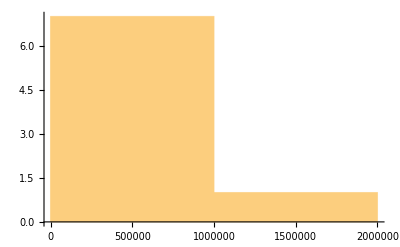

```mathematica
Histogram[{0,13192,0,0,0,0,0,1910808}]
```

```mathematica
dprop[x_]:=Block[{g=Quiet[GraphData[RandomChoice[lt30]]]},
Block[{g1=Graph[Map[Piecewise[{{#[[1]]->#[[2]], RandomInteger[1]==0}, {#[[2]]->#[[1]], True}}]&,EdgeList[g]]]},


Block[{vc1=VertexConnectivity[g1],ec1=VertexConnectivity[g1],vc2=VertexConnectivity[g2],ec2=VertexConnectivity[g2]},
Block[{numcy1=Length[FindCycle[g1,∞,All]],numcy2=Length[FindCycle[g2,∞,All]]},
Map[Boole,{(vc1==vc2)||((vc1<vc2)&&(numcy1≤numcy2))||((vc1>vc2)&&(numcy1≥numcy2)),
(ec1==ec2)||((ec1<ec2)&&(numcy1≤numcy2))||((ec1>ec2)&&(numcy1≥numcy2)),
(¬((vc1<vc2)&&(ec1<ec2))||¬((vc1>vc2)&&(ec1>ec2)))||((vc1<vc2)&&(ec1<ec2)&&(numcy1≤numcy2))||((vc1>vc2)&&(ec1>ec2)&&(numcy1≥numcy2))}]]]]]
```

```mathematica
found=False;
i=0;
While[¬found&&i<2^maxdist,
```

```mathematica
max=4;
```

```mathematica
doubles=Flatten[Table[Table[{i,j},{i,0,j-1}],{j,1,max}],1]
Length[%]
Binomial[max+1,2]
```

{{0,1},{0,2},{1,2},{0,3},{1,3},{2,3},{0,4},{1,4},{2,4},{3,4}}

10

10

```mathematica
triples=Flatten[Table[Table[Table[{i,j,k},{i,0,j-1}],{j,1,k-1}],{k,2,max}],2]
Length[%]
Binomial[max+1,3]
```

{{0,1,2},{0,1,3},{0,2,3},{1,2,3},{0,1,4},{0,2,4},{1,2,4},{0,3,4},{1,3,4},{2,3,4}}

10

10

```mathematica
nuples

Flatten[Table[Table[Table[{i,j,k},{i,0,j-1}],{j,1,k-1}],{k,2,max}],2]
```

```mathematica
setnth[int_,pos_]:=BitOr[int,2^pos]
setnths[int_,pos_]:=Fold[BitOr[#1,2^#2]&,int,pos]
orientgraph[graph_,x_]:=Block[{el=EdgeList[graph],len=EdgeCount[graph]},Block[{xs=PadLeft[IntegerDigits[x,2],len]},Graph[Table[Piecewise[{{el[[i]][[1]]->el[[i]][[2]], xs[[i]]==0}, {el[[i]][[2]]->el[[i]][[1]], True}}],{i,1,len}]]]]
numcy[g_]:=Length[FindCycle[g,∞,All]]
```

```mathematica
gr=CompleteGraph[5];
numes=EdgeCount[gr];
ncyos=Monitor[Table[Block[{o=orientgraph[gr,j]},{numcy[o],j}],{j,0,2^numes-1}],j];
```

```mathematica
hammingDistance[x_,y_]:=popcnt[BitXor[x,y]]
popcnt[x0_]:=Block[{x=x0,count=0},While[x≠0,count+=BitAnd[x,1];x=BitShiftRight[x]];count]
popcnt[3]
closests[o_,os_]:=
Block[{ncyo=First[o],valo=Last[o]},
Block[{betters=Select[os,First[#]>ncyo&]},
Block[{betterswdist=Map[{hammingDistance[valo,Last[#]],First[#],Last[#]}&,betters]},
Block[{mindist=Min[Map[First,betterswdist]]},
Join[{Prepend[o,0]},Select[betterswdist,First[#]==mindist&]]]]]]
```

2

```mathematica
results=Monitor[Table[closests[ncyos[[k]],ncyos],{k,1,Length[ncyos]}],k];
```

```mathematica
Map[Piecewise[{{1, Length[#]==1}, {First[#[[2]]], True}}]&,results]
```

```mathematica
gr2=CompleteGraph[4];
numes2=EdgeCount[gr2];
ncyos2=Monitor[Table[Block[{o=orientgraph[gr2,j]},{numcy[o],j}],{j,0,2^numes2-1}],j];
```

```mathematica
results2=Monitor[Table[closests[ncyos2[[k]],ncyos2],{k,1,Length[ncyos2]}],k];
```

```mathematica
dists2=Map[Piecewise[{{1, Length[#]==1}, {First[#[[2]]], True}}]&,results2];
```

```mathematica
Tally[dists2]
```

{{1,64}}

```mathematica
gr3=PetersenGraph[];
numes3=EdgeCount[gr3];
2^%
ncyos3=Monitor[Table[Block[{o=orientgraph[gr3,j]},{numcy[o],j}],{j,0,2^numes3-1}],j];
```

32768

```mathematica
pcounter=1;
SetSharedVariable[pcounter];
ParallelEvaluate[last=AbsoluteTime[];plocalcounter=1;]
results3=Timing[Monitor[ParallelTable[plocalcounter++;
If[AbsoluteTime[]-last>1,last=AbsoluteTime[];
pcounter+=plocalcounter;plocalcounter=0;];closests[ncyos3[[n]],ncyos3],{n,1,Length[ncyos3]}],ProgressIndicator[pcounter,{1,Length[ncyos3]}]]];
Clear[pcounter];
```

{Null,Null,Null,Null,Null,Null}

```mathematica
dists3=Map[Piecewise[{{1, Length[#]==1}, {First[#[[2]]], True}}]&,results3[[2]]];
```

```mathematica
Tally[dists3]
```

{{1,31208},{2,1560}}

```mathematica
First[results3]
```

630.853

```mathematica
getResults[gri_]:=
Block[{numesi=EdgeCount[gri]},
Block[{ncyosi=Monitor[Table[Block[{o=orientgraph[gri,j]},{numcy[o],j}],{j,0,2^numesi-1}],j],pcounter=1},
SetSharedVariable[pcounter];
ParallelEvaluate[last=AbsoluteTime[];plocalcounter=1;];
Block[{resultsi=Timing[Monitor[ParallelTable[plocalcounter++;
If[AbsoluteTime[]-last>1,last=AbsoluteTime[];
pcounter+=plocalcounter;plocalcounter=0;];closests[ncyosi[[n]],ncyosi],{n,1,Length[ncyosi]}],ProgressIndicator[pcounter,{1,Length[ncyosi]}]]]},
Print[resultsi[[1]]];
Block[{rs=resultsi[[2]]},
Block[{distsi=Map[Piecewise[{{1, Length[#]==1}, {First[#[[2]]], True}}]&,rs]},
{Max[Map[Last[#][[2]]&,rs]],Tally[distsi]}]]]]]
```

```mathematica
getResults[CompleteGraph[4]]
```

0.025897

{3,{{1,64}}}

```mathematica
Monitor[Table[getResults[GraphData[lt30[[m]]]],{m,1,45}],m]
```

0.389508

0.412284

2.09129

9.42452

8.91729

8.69734

8.73547

8.71193

9.15582

8.89644

8.89853

9.5043

8.7636

9.30875

7.89215

7.72941

7.68024

2.18913

2.39849

1.9192

1.97676

2.01631

8.91341

9.34447

9.02296

8.66175

0.490184

2.11002

9.15753

0.148038

2.10097

7.94423

2.32532

8.71766

0.464824

0.124937

8.21058

9.1164

9.14035

0.021804

0.122961

7.79193

0.055098

0.497253

9.24711

{{7,{{1,1024}}},{9,{{1,988},{3,36}}},{12,{{1,1992},{2,32},{3,24}}},{12,{{1,3992},{2,104}}},{10,{{1,4062},{2,34}}},{10,{{1,4072},{2,24}}},{12,{{1,4016},{2,52},{3,22},{4,6}}},{11,{{1,4022},{2,62},{3,12}}},{12,{{1,4072},{2,24}}},{15,{{1,4040},{2,44},{3,12}}},{12,{{1,4016},{2,52},{3,20},{4,8}}},{17,{{1,4016},{2,48},{3,32}}},{10,{{2,112},{1,3984}}},{15,{{1,3988},{2,108}}},{8,{{1,3992},{5,8},{2,92},{3,4}}},{7,{{1,4044},{2,52}}},{7,{{2,134},{1,3932},{3,24},{4,6}}},{13,{{1,1978},{2,58},{3,12}}},{10,{{1,2030},{2,18}}},{7,{{1,2040},{2,8}}},{8,{{1,1992},{2,40},{4,4},{3,12}}},{8,{{1,1994},{3,14},{2,32},{5,8}}},{11,{{1,4004},{2,62},{3,10},{4,12},{5,8}}},{13,{{1,4012},{3,20},{2,64}}},{13,{{1,4046},{2,44},{3,6}}},{12,{{1,4046},{2,26},{3,16},{4,8}}},{8,{{1,988},{2,20},{3,16}}},{12,{{1,1996},{3,24},{2,28}}},{16,{{1,4052},{2,36},{3,8}}},{8,{{1,476},{2,24},{3,12}}},{12,{{1,1968},{2,80}}},{9,{{1,4024},{2,72}}},{9,{{1,1976},{2,72}}},{18,{{1,3982},{2,84},{4,12},{3,18}}},{12,{{1,984},{2,40}}},{5,{{1,464},{2,36},{3,12}}},{11,{{1,4072},{3,12},{2,12}}},{12,{{1,4042},{3,12},{2,42}}},{11,{{1,4000},{2,84},{3,12}}},{3,{{1,64}}},{5,{{2,32},{1,480}}},{7,{{1,4000},{2,80},{3,16}}},{5,{{1,246},{2,10}}},{7,{{1,1024}}},{10,{{1,4058},{2,38}}}}

```mathematica
Column[%]
```

{7,{{1,1024}}}
{9,{{1,988},{3,36}}}
{12,{{1,1992},{2,32},{3,24}}}
{12,{{1,3992},{2,104}}}
{10,{{1,4062},{2,34}}}
{10,{{1,4072},{2,24}}}
{12,{{1,4016},{2,52},{3,22},{4,6}}}
{11,{{1,4022},{2,62},{3,12}}}
{12,{{1,4072},{2,24}}}
{15,{{1,4040},{2,44},{3,12}}}
{12,{{1,4016},{2,52},{3,20},{4,8}}}
{17,{{1,4016},{2,48},{3,32}}}
{10,{{2,112},{1,3984}}}
{15,{{1,3988},{2,108}}}
{8,{{1,3992},{5,8},{2,92},{3,4}}}
{7,{{1,4044},{2,52}}}
{7,{{2,134},{1,3932},{3,24},{4,6}}}
{13,{{1,1978},{2,58},{3,12}}}
{10,{{1,2030},{2,18}}}
{7,{{1,2040},{2,8}}}
{8,{{1,1992},{2,40},{4,4},{3,12}}}
{8,{{1,1994},{3,14},{2,32},{5,8}}}
{11,{{1,4004},{2,62},{3,10},{4,12},{5,8}}}
{13,{{1,4012},{3,20},{2,64}}}
{13,{{1,4046},{2,44},{3,6}}}
{12,{{1,4046},{2,26},{3,16},{4,8}}}
{8,{{1,988},{2,20},{3,16}}}
{12,{{1,1996},{3,24},{2,28}}}
{16,{{1,4052},{2,36},{3,8}}}
{8,{{1,476},{2,24},{3,12}}}
{12,{{1,1968},{2,80}}}
{9,{{1,4024},{2,72}}}
{9,{{1,1976},{2,72}}}
{18,{{1,3982},{2,84},{4,12},{3,18}}}
{12,{{1,984},{2,40}}}
{5,{{1,464},{2,36},{3,12}}}
{11,{{1,4072},{3,12},{2,12}}}
{12,{{1,4042},{3,12},{2,42}}}
{11,{{1,4000},{2,84},{3,12}}}
{3,{{1,64}}}
{5,{{2,32},{1,480}}}
{7,{{1,4000},{2,80},{3,16}}}
{5,{{1,246},{2,10}}}
{7,{{1,1024}}}
{10,{{1,4058},{2,38}}}

```mathematica
Length[lt30]
```

45

```mathematica
lt30
```

{{6,114},{6,130},{6,149},{7,550},{7,737},{7,763},{7,839},{7,888},{7,934},{7,956},{7,963},{BiggestLittlePolygon,6},{CompleteBipartite,{3,4}},{Cone,{3,3}},{Cubic,{8,2}},{Cubic,{8,3}},CubicalGraph,{Fan,{2,4}},{Fan,{3,3}},{Harary,{3,7}},{Heptahedral,2},{Heptahedral,7},{Heptahedral,8},{Heptahedral,18},{Heptahedral,21},{Heptahedral,25},{Hexahedral,3},{Hexahedral,4},{Hexahedral,5},{JohnsonSkeleton,12},{King,{2,3}},{Matchstick,3},MoserSpindle,OctahedralGraph,PentatopeGraph,{Prism,3},SelfDualGraph1,SelfDualGraph2,SelfDualGraph3,TetrahedralGraph,UtilityGraph,WagnerGraph,{Wheel,5},{Wheel,6},{Wheel,7}}

```mathematica
Map[GraphData,lt30]
```

```mathematica
lt30[[22]]
lt30[[23]]
```

{Heptahedral,7}

```mathematica
Map[{#,GraphData[{"Heptahedral",7},#]}&,GraphData[{"Heptahedral",7},"Properties"]]
```

```mathematica
Position[Table[7 #1+19 #1^2+21 #1^3+13 #1^4+5 #1^5+#1^6+7 #2+29 #1 #2+30 #1^2 #2+12 #1^3 #2+2 #1^4 #2+17 #2^2+26 #1 #2^2+7 #1^2 #2^2+15 #2^3+6 #1 #2^3+6 #2^4+#2^5&[i,j],{i,-5,5},{j,-5,5}],6]
```

{{4,6}}

```mathematica
Table[7 #1+19 #1^2+21 #1^3+13 #1^4+5 #1^5+#1^6+7 #2+29 #1 #2+30 #1^2 #2+12 #1^3 #2+2 #1^4 #2+17 #2^2+26 #1 #2^2+7 #1^2 #2^2+15 #2^3+6 #1 #2^3+6 #2^4+#2^5&[i,j],{i,-2,-2},{j,0,0}]
```

{{6}}

```mathematica
Map[{#,GraphData[{"Heptahedral",8},#]}&,GraphData[{"Heptahedral",8},"Properties"]]
```

```mathematica
GraphData[{"Heptahedral",8}]
```

```mathematica
GraphData[{"Heptahedral",7}]
```

```mathematica
props=Intersection@@Map[GraphData[#,"Properties"]&,lt30];
Length[props]
```

457

```mathematica
alrs=Out[15];
```

```mathematica
rnums=Map[First,Map[Last,Map[Sort,Map[Last,alrs]]]]
```

{1,3,3,2,2,2,4,3,2,3,4,3,2,2,5,2,4,3,2,2,4,5,5,3,3,4,3,3,3,3,2,2,2,4,2,3,3,3,3,1,2,3,2,1,2}

```mathematica
Length[props]
```

457

```mathematica
pr++
```

22

```mathematica
props[[128]]
```

DetourIndex

```mathematica
props[[130]]
```

DetourPolynomial

```mathematica
props[[131]]
```

Diameter

```mathematica
props[[235]]
```

IndependenceNumber

```mathematica
props[[304]]
```

MeanDistance

```mathematica
Position[props,"DistanceMatrix"]
```

{{143}}

```mathematica
pr=143;
```

```mathematica
pr=131;
Sort[Table[{rnums[[i]],MatrixForm[GraphData[lt30[[i]],props[[128]]]],MatrixForm[GraphData[lt30[[i]],props[[131]]]],MatrixForm[GraphData[lt30[[i]],props[[235]]]],N[MatrixForm[GraphData[lt30[[i]],props[[304]]]]]},{i,1,Length[rnums]}]]//TableForm
```

1 | 18 | 1 | 1 | 0.75
1 | 72 | 2 | 3 | 1.11111
1 | 75 | 2 | 2 | 1.11111
2 | 40 | 1 | 1 | 0.8
2 | 40 | 2 | 2 | 0.96
2 | 69 | 2 | 3 | 1.16667
2 | 72 | 2 | 3 | 1.
2 | 72 | 2 | 3 | 1.05556
2 | 73 | 2 | 2 | 1.05556
2 | 108 | 2 | 4 | 1.22449
2 | 122 | 2 | 2 | 1.22449
2 | 122 | 2 | 2 | 1.26531
2 | 122 | 2 | 3 | 1.22449
2 | 123 | 2 | 3 | 1.22449
2 | 123 | 2 | 3 | 1.22449
2 | 123 | 2 | 3 | 1.26531
2 | 126 | 2 | 3 | 1.22449
2 | 186 | 3 | 3 | 1.5625
2 | 192 | 2 | 3 | 1.375
3 | 40 | 2 | 2 | 0.88
3 | 73 | 2 | 2 | 1.11111
3 | 75 | 2 | 2 | 1.
3 | 75 | 2 | 2 | 1.
3 | 75 | 2 | 2 | 1.05556
3 | 75 | 2 | 2 | 1.05556
3 | 75 | 2 | 2 | 1.05556
3 | 75 | 2 | 2 | 1.11111
3 | 75 | 2 | 2 | 1.16667
3 | 123 | 2 | 3 | 1.22449
3 | 124 | 2 | 2 | 1.22449
3 | 126 | 2 | 2 | 1.22449
3 | 126 | 2 | 2 | 1.22449
3 | 126 | 2 | 3 | 1.22449
3 | 126 | 2 | 3 | 1.22449
3 | 126 | 2 | 3 | 1.22449
3 | 196 | 2 | 3 | 1.375
4 | 75 | 2 | 2 | 1.
4 | 126 | 2 | 3 | 1.22449
4 | 126 | 2 | 3 | 1.22449
4 | 126 | 2 | 3 | 1.22449
4 | 126 | 2 | 3 | 1.26531
4 | 184 | 3 | 4 | 1.5
5 | 126 | 2 | 3 | 1.22449
5 | 126 | 2 | 3 | 1.26531
5 | 196 | 3 | 3 | 1.4375

```mathematica
pr=442;
Sort[Table[{rnums[[i]],N[x/.Solve[rnums[[i]]==GraphData[lt30[[i]],props[[pr]]][x],x]]},{i,1,Length[rnums]}]]//Column
```

{1,{-0.292893-0.573086 ⅈ,-0.292893+0.573086 ⅈ,-4.01545,0.601232}}
{1,{-5.04929,0.556258,-0.823768-0.41537 ⅈ,-0.823768+0.41537 ⅈ,0.0702833-0.64294 ⅈ,0.0702833+0.64294 ⅈ}}
{1,{-5.0004,0.580298,-0.888847-0.295106 ⅈ,-0.888847+0.295106 ⅈ,0.0988982-0.618963 ⅈ,0.0988982+0.618963 ⅈ}}
{2,{-4.99679,-0.832307,0.767384,0.0308574-0.791026 ⅈ,0.0308574+0.791026 ⅈ}}
{2,{-1.,-0.069285-0.791694 ⅈ,-0.069285+0.791694 ⅈ,-4.55642,0.694989}}
{2,{-5.48686,0.685769,-0.754799-0.530544 ⅈ,-0.754799+0.530544 ⅈ,0.155343-0.774802 ⅈ,0.155343+0.774802 ⅈ}}
{2,{-5.2786,0.669435,-0.823666-0.520769 ⅈ,-0.823666+0.520769 ⅈ,0.128249-0.761286 ⅈ,0.128249+0.761286 ⅈ}}
{2,{-5.23666,0.693581,-0.879169-0.45825 ⅈ,-0.879169+0.45825 ⅈ,0.150709-0.733146 ⅈ,0.150709+0.733146 ⅈ}}
{2,{-4.84828,0.622314,-0.945132-0.532037 ⅈ,-0.945132+0.532037 ⅈ,0.0581144-0.74842 ⅈ,0.0581144+0.74842 ⅈ}}
{2,{-5.53004,-1.10423,0.605409,-0.673659-0.767977 ⅈ,-0.673659+0.767977 ⅈ,0.188093-0.694989 ⅈ,0.188093+0.694989 ⅈ}}
{2,{-5.40257,-1.42328,0.651387,-0.656885-0.61121 ⅈ,-0.656885+0.61121 ⅈ,0.244114-0.660597 ⅈ,0.244114+0.660597 ⅈ}}
{2,{-5.40257,-1.42328,0.651387,-0.656885-0.61121 ⅈ,-0.656885+0.61121 ⅈ,0.244114-0.660597 ⅈ,0.244114+0.660597 ⅈ}}
{2,{-5.40257,-1.42328,0.651387,-0.656885-0.61121 ⅈ,-0.656885+0.61121 ⅈ,0.244114-0.660597 ⅈ,0.244114+0.660597 ⅈ}}
{2,{-5.40257,-1.42328,0.651387,-0.656885-0.61121 ⅈ,-0.656885+0.61121 ⅈ,0.244114-0.660597 ⅈ,0.244114+0.660597 ⅈ}}
{2,{-5.30264,-1.73306,0.675811,-0.594271-0.546345 ⅈ,-0.594271+0.546345 ⅈ,0.274217-0.647289 ⅈ,0.274217+0.647289 ⅈ}}
{2,{-5.18179,-1.50378,0.633696,-0.696056-0.600729 ⅈ,-0.696056+0.600729 ⅈ,0.221993-0.655617 ⅈ,0.221993+0.655617 ⅈ}}
{2,{-4.99979,-2.01996,0.667293,-0.589549-0.519536 ⅈ,-0.589549+0.519536 ⅈ,0.265775-0.640291 ⅈ,0.265775+0.640291 ⅈ}}
{2,{-4.90328,-2.80388,-0.852378,0.644994,-0.37909-0.663051 ⅈ,-0.37909+0.663051 ⅈ,0.336362-0.583487 ⅈ,0.336362+0.583487 ⅈ}}
{2,{-1.,-5.16429,-2.2193,0.62813,-0.435994-0.665532 ⅈ,-0.435994+0.665532 ⅈ,0.313725-0.583477 ⅈ,0.313725+0.583477 ⅈ}}
{3,{-1.,-0.0112423-0.880889 ⅈ,-0.0112423+0.880889 ⅈ,-4.78531,0.80779}}
{3,{-5.45018,0.7763,-0.861602-0.532696 ⅈ,-0.861602+0.532696 ⅈ,0.198544-0.807208 ⅈ,0.198544+0.807208 ⅈ}}
{3,{-5.45018,0.7763,-0.861602-0.532696 ⅈ,-0.861602+0.532696 ⅈ,0.198544-0.807208 ⅈ,0.198544+0.807208 ⅈ}}
{3,{-5.23696,0.757369,-0.933039-0.512196 ⅈ,-0.933039+0.512196 ⅈ,0.172834-0.798602 ⅈ,0.172834+0.798602 ⅈ}}
{3,{-5.23696,0.757369,-0.933039-0.512196 ⅈ,-0.933039+0.512196 ⅈ,0.172834-0.798602 ⅈ,0.172834+0.798602 ⅈ}}
{3,{-5.23696,0.757369,-0.933039-0.512196 ⅈ,-0.933039+0.512196 ⅈ,0.172834-0.798602 ⅈ,0.172834+0.798602 ⅈ}}
{3,{-5.0012,0.740274,-1.01944-0.470542 ⅈ,-1.01944+0.470542 ⅈ,0.149897-0.787593 ⅈ,0.149897+0.787593 ⅈ}}
{3,{-5.0012,0.740274,-1.01944-0.470542 ⅈ,-1.01944+0.470542 ⅈ,0.149897-0.787593 ⅈ,0.149897+0.787593 ⅈ}}
{3,{-4.73377,0.724746,-1.12538-0.386934 ⅈ,-1.12538+0.386934 ⅈ,0.129896-0.77497 ⅈ,0.129896+0.77497 ⅈ}}
{3,{-5.44933,-1.31605,0.693798,-0.719682-0.724027 ⅈ,-0.719682+0.724027 ⅈ,0.255474-0.716437 ⅈ,0.255474+0.716437 ⅈ}}
{3,{-5.35367,-1.60492,0.71618,-0.664476-0.634152 ⅈ,-0.664476+0.634152 ⅈ,0.285681-0.704443 ⅈ,0.285681+0.704443 ⅈ}}
{3,{-5.35367,-1.60492,0.71618,-0.664476-0.634152 ⅈ,-0.664476+0.634152 ⅈ,0.285681-0.704443 ⅈ,0.285681+0.704443 ⅈ}}
{3,{-5.35367,-1.60492,0.71618,-0.664476-0.634152 ⅈ,-0.664476+0.634152 ⅈ,0.285681-0.704443 ⅈ,0.285681+0.704443 ⅈ}}
{3,{-5.30258,-1.74883,0.728414,-0.638158-0.603731 ⅈ,-0.638158+0.603731 ⅈ,0.299653-0.696923 ⅈ,0.299653+0.696923 ⅈ}}
{3,{-5.30258,-1.74883,0.728414,-0.638158-0.603731 ⅈ,-0.638158+0.603731 ⅈ,0.299653-0.696923 ⅈ,0.299653+0.696923 ⅈ}}
{3,{-5.30258,-1.74883,0.728414,-0.638158-0.603731 ⅈ,-0.638158+0.603731 ⅈ,0.299653-0.696923 ⅈ,0.299653+0.696923 ⅈ}}
{3,{-5.23612,-1.9747,-1.16971,0.667995,-0.477202-0.718879 ⅈ,-0.477202+0.718879 ⅈ,0.33347-0.622539 ⅈ,0.33347+0.622539 ⅈ}}
{4,{-5.45041,0.825081,-0.903648-0.569794 ⅈ,-0.903648+0.569794 ⅈ,0.216315-0.855919 ⅈ,0.216315+0.855919 ⅈ}}
{4,{-5.40245,-1.48848,0.744792,-0.718309-0.720187 ⅈ,-0.718309+0.720187 ⅈ,0.291381-0.748736 ⅈ,0.291381+0.748736 ⅈ}}
{4,{-5.35361,-1.62573,0.756099,-0.693983-0.680101 ⅈ,-0.693983+0.680101 ⅈ,0.305605-0.741887 ⅈ,0.305605+0.741887 ⅈ}}
{4,{-5.35361,-1.62573,0.756099,-0.693983-0.680101 ⅈ,-0.693983+0.680101 ⅈ,0.305605-0.741887 ⅈ,0.305605+0.741887 ⅈ}}
{4,{-5.06406,-1.88376,0.747588,-0.696378-0.64053 ⅈ,-0.696378+0.64053 ⅈ,0.296493-0.73391 ⅈ,0.296493+0.73391 ⅈ}}
{4,{-5.20923,-2.19174,-1.05598,0.687631,-0.458252-0.802559 ⅈ,-0.458252+0.802559 ⅈ,0.342907-0.668826 ⅈ,0.342907+0.668826 ⅈ}}
{5,{-5.4024,-1.51434,0.777321,-0.738391-0.758069 ⅈ,-0.738391+0.758069 ⅈ,0.308098-0.779201 ⅈ,0.308098+0.779201 ⅈ}}
{5,{-5.12446,-1.74311,0.769138,-0.749882-0.709498 ⅈ,-0.749882+0.709498 ⅈ,0.299096-0.770349 ⅈ,0.299096+0.770349 ⅈ}}
{5,{-5.08625,-2.41623,-1.09114,0.739487,-0.4579-0.789975 ⅈ,-0.4579+0.789975 ⅈ,0.384967-0.675704 ⅈ,0.384967+0.675704 ⅈ}}

```mathematica
Map[EdgeCount[GraphData[#]]&,lt30]
```

{10,10,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,12,12,12,12,10,11,12,9,11,12,11,12,10,9,12,12,12,6,9,12,8,10,12}

```mathematica
results2
```

```mathematica
Drop[{1,2,3},1]
```

{2,3}

```mathematica
checkg1[g_]:=Block[{len=EdgeCount[g]},
Block[{start=RandomInteger[{0,2^len-1}]},
Max[Map[numcy[orientgraph[g,setnth[start,#]]]&,Range[0,len-1]]]>numcy[orientgraph[g,start]]]]
```

```mathematica
checkgn[g_,n_]:=Block[{len=EdgeCount[g]},
Block[{start=RandomInteger[{0,2^len-1}]},
Max[Map[numcy[orientgraph[g,setnths[start,#]]]&,Select[Tuples[Map[Range,ConstantArray[len,n]]],Length[DeleteDuplicates[#]]==Length[#]&]]]>numcy[orientgraph[g,start]]]]
```

```mathematica
Timing[checkgn[CompleteGraph[5],3]]
```

{0.116432,False}

```mathematica
checkgnm[g_,n_,m_]:=Total[Map[Boole[checkgn[g,n]]&,Range[m]]]
checkgnm[CompleteGraph[3],3,15]
```

1

```mathematica
Length[lt30]
```

1546

```mathematica
ParallelTable[Boole[checkg[GraphData[lt30[[i]]]]],{i,1,1546}]
```